```mathematica
John's dirt-simple self-contained liquid-phase NMR simulator

Mathematica version

Homonuclear spin-1/2,scalar J-coupling and chemical shift, 1-d FID and spectrum with exponential apodization

The size of the interaction matrix determines the number of spins

Thanks to Ilya Kuprov for helpful examples. See his web site spindynamics.org and watch his YouTube lectures

john.price@colorado.edu

Computation Section
```

```mathematica
(*Control Parameters*)
fL=45.0;                          (*Larmor frequency in MHz. Used only to convert frequencies from ppm to Hz*)
samplingRate=3000;   (*Sampling rate in Hz or 1/(simulation time step)*)
steps=3000;                   (*Number of time steps*)
zeroFill=4*steps;    (*Zero-fill the FID to this many samples before FFT*)
T2=0.3;                            (*T2 time constant in seconds, the FID decays with this time constant*)
phase=0.0;                     (*Phase of spectrum to plot in radians, real part is 0, imaginary part is pi/2*)

(*Interaction matrix
An NxN real matrix where N is the number of spins to be simulated
N must be less than 12 on a typical workstation
N must be less than 20 unless you have a quantum computer

Diagonal elements are the Zeeman (chemical shift) coefficients in ppm

Elements below the diagonal are scalar J-coupling coefficients in Hz
For example,the number in the fouth row and second column is the
coupling between spin 2 and spin 4 in Hz

Elements above the diagonal are not used*)

(*Example:very dry ethanol showing non-exchanging OH proton
spins:   CH3   CH3    CH3    CH2   CH2   OH*)
inter={{1.1 ,   0,         0,         0,       0,         0},
           {0 ,       1.1,     0,         0,       0,         0},
           {0 ,       0,         1.1,     0,       0,         0},
           {6.81, 6.81,  6.81,    3.6,   0,         0},
           {6.81, 6.81,  6.81,    0,       3.6,     0},
            {0 ,       0,        0,          5.37,  5.37,  5.3}};

nspins=Length[inter];  (*find the number of spins*)

(*Define the Pauli spin matrices and a unit matrix
Include factor of 1/2 for correct spin-1/2 eigenvalues*)
sigmaX=(1/2)*{{0,1},{1,0}};
sigmaY=(1/2)*{{0,-I},{I,0}};
sigmaZ=(1/2)*{{1,0},{0,-1}};
unit={{1,0},{0,1}};

(*Build the single-spin operators Sx[[i]],Sy[[i]],Sz[[i]]
The index i labels which spin it operates on
These are direct or Kronecker products of Pauli and unit matricies
For example,Sy for the third spin in a four-spin system is
unit (x) unit (x) sigma_y (x) unit  *)
Sx={}; Sy={}; Sz={};
For[i=1,i<=nspins,i++,         (*which spin it acts on*)
SxCurrent={1}; SyCurrent={1}; SzCurrent={1};
For[k=1,k≤nspins, k++,        (*loop over all spins*)
If[ k==i,                     (*Kronecker in a Pauli matrix if this is the spin its acting on*)
SxCurrent=KroneckerProduct[SxCurrent,N[sigmaX]];
SyCurrent=KroneckerProduct[SyCurrent,N[sigmaY]];
SzCurrent=KroneckerProduct[SzCurrent,N[sigmaZ]],
                                         (*else Kronecker in a unit matrix*)
SxCurrent=KroneckerProduct[SxCurrent,unit];
SyCurrent=KroneckerProduct[SyCurrent,unit];
SzCurrent=KroneckerProduct[SzCurrent,unit]]
];
Sx=Join[Sx,{SxCurrent}]; Sy=Join[Sy,{SyCurrent}]; Sz=Join[Sz,{SzCurrent}]
]

(*Build magnetization operators
These are sums over all spins of the single-spin operators*)
Mx=My=Mz=ConstantArray[0,{2^nspins,2^nspins}];
For[i=1,i≤nspins,i++,
Mx=Mx+ Sx[[i]];
My=My+ Sy[[i]];
Mz=Mz+ Sz[[i]]
]

(*Build the Hamiltonian (in rad/s units)*)
H=ConstantArray[0,{2^nspins,2^nspins}];
For[i=1,i≤nspins,i++,
For[k=1,k≤nspins, k++,
If[i==k,
H=H+2*π*fL*inter[[i,k]]*Sz[[i]],                   (*Zeeman terms*)
If[i>k,
H=H+2*π*inter[[i,k]]*(Sx[[i]].Sx[[k]]+Sy[[i]].Sy[[k]]+Sz[[i]].Sz[[k]])   (*J-coupling terms*)
]]]]

(*Define the observable*)
obs=Mx + I*My;         (*Mx is real part,My is imaginary part*)

(*Initialize the density matrix rho to Mx*)
rho=Mx;                                        

(*Propagator*)
timeStep=1/samplingRate;
P=MatrixExp[-I*H*timeStep];          (*Mathematica's matrix exponential*)

(*Evolve the system and compute the observable
The FID is the free-induction-decay, a complex time series*)
FID=ConstantArray[0,steps];
For [n=1, n⩽steps,n++,
FID[[n]]=Tr[obs.rho];                        (*Mathematica's matrix trace*)
rho=P.rho.ConjugateTranspose[P];
If[Mod[n,200]==0, Print["step ", n]];    (*Report progress*)
]

(*Apodization (filtering) to simulate relaxation
Multiply the FID by an exponential decay with time constant T2*)
duration=steps*timeStep;
windowFunction=Exp[-(duration/T2)*Range[0,1,N[1/(steps-1)]]];
winFID=FID*windowFunction;

(*FFT with zero-filling
Zero-filling has the effect of interpolating between frequency points
which makes the spectrum smoother*)
spectrum=Fourier[Catenate[{winFID,ConstantArray[0,zeroFill-steps]}],FourierParameters->{1,-1}];  (*Use MATLAB's FFT conventions*)
spectrumSwapped=Catenate[ {spectrum[[zeroFill/2+1;;zeroFill]],spectrum[[1;;zeroFill/2]] }];             (*Mathematica's FFT needs to be rearranged*)
timeSeries=Range[0,duration,N[duration/(steps-1)]];                                                                                                           (*in seconds*)
freqSeries=Range[N[-1/(2*timeStep)],N[1/(2*timeStep)],N[1/(timeStep*(zeroFill-1))]];                         (*in Hz*)
```

step 200

step 400

step 600

step 800

step 1000

step 1200

step 1400

step 1600

step 1800

step 2000

step 2200

step 2400

step 2600

step 2800

step 3000

```mathematica
Plotting Section
```

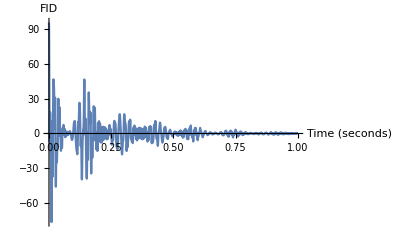

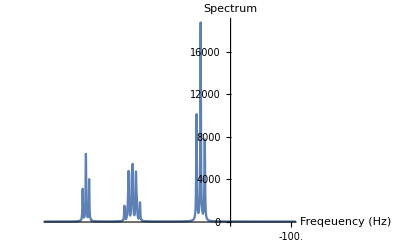

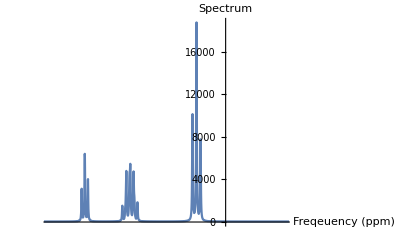

```mathematica
plotMinFreq=-100;    (*Frequency range in Hz for spectrum plots*)
plotMaxFreq=300;

(*Real part of the apodized FID*)
ListLinePlot[Re[Transpose[{timeSeries,winFID}]],PlotRange->All,                                    
AxesLabel->{"Time (seconds)", "FID"}]

(* Plot spectrum in Hz. NMR spectra are plotted with the frequency axis backwards*)
ListLinePlot[Re[Transpose[{-freqSeries,Exp[I*phase]*spectrumSwapped}]],PlotRange->{{-plotMaxFreq,-plotMinFreq},All},
 Ticks->{Table[{-i,i},{i,First[freqSeries],Last[freqSeries],100}],Automatic},
AxesLabel->{"Freqeuency (Hz)", "Spectrum"} ]

(*Plot spectrum in ppm. NMR spectra are plotted with the frequency axis backwards*)
ListLinePlot[Re[Transpose[{-freqSeries/fL,Exp[I*phase]*spectrumSwapped}]],PlotRange->{{-plotMaxFreq/fL,-plotMinFreq/fL},All},
 Ticks->{Table[{-i,i},{i,First[freqSeries],Last[freqSeries],1}],Automatic},
AxesLabel->{"Freqeuency (ppm)", "Spectrum"}]
```